# Terminal Velocity

```mathematica
(* The net Force *)
m g - β m g f[v]
(* β is the retardation ratio *)
```

```mathematica
(* f[v]= v *)
DSolve[ {v'[t]== 1 - β v[t],v[0]==0},v[t],t]//Expand
```

{{v[t]→1/β-ⅇ^(-t β)/β}}

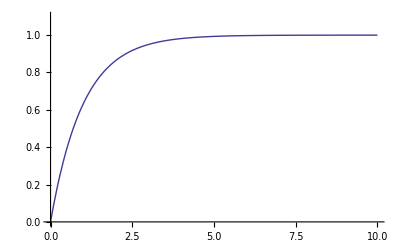

```mathematica
Plot[(1-Exp[-t]),{t,0,10},PlotRange->{0,1.1}]
```

```mathematica
(* f[v]= v^2 *)
DSolve[ {v'[t]== 1 - β (v[t])^2,v[0]==0},v[t],t]//Expand
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→Tanh[t √β]/(√β)}}

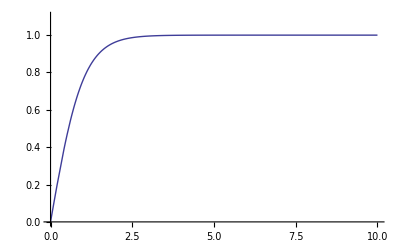

```mathematica
Plot[Tanh[t],{t,0,10},PlotRange->{0,1.1}]
```

```mathematica
(* f[v]= v^2 *)
DSolve[ {v'[t]== 1 - β (v[t])^3},v[t],t]//Expand
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

{{v[t]→InverseFunction[-1/(6 β^(1/3))(2 √3 ArcTan[(1+2 β^(1/3) #1)/(√3)]-2 Log[-1+β^(1/3) #1]+Log[1+β^(1/3) #1+β^(2/3) #1^2])&][-t+C[1]]}}

```mathematica
(* Compare *)
Manipulate[
Plot[{1/β-ⅇ^(-t β)/β,Tanh[t √β]/(√β)},{t,0,10},PlotRange->{0,2},PlotStyle->{Red, Blue}],
{{β,1},0,2}]
```